```mathematica
Clear["Global`*"];
λ0=1;
w0=.5; (*tightly focused*)
λ=λ0/n;
n=1;

zR=(π w0^2)/λ;
w[z_]:=w0 √(1+ ((λ z)/(π w0^2))^2);
R[z_]:=z(1+((π w0^2)/(λ z))^2);
qInv[z_]:=1/R[z]-I λ0/(π  n  w[z]^2);

q[z_]:=z+zR I;
```

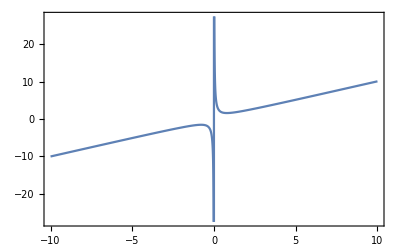

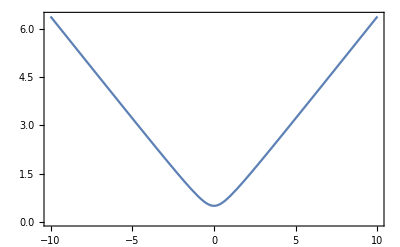

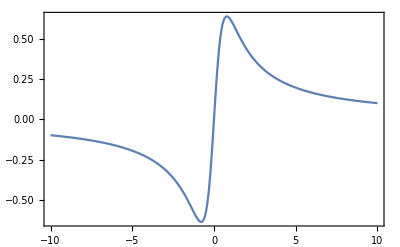

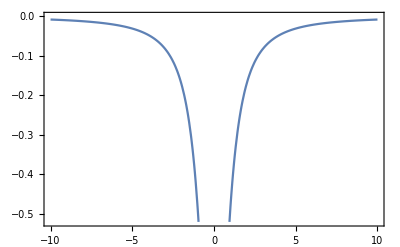

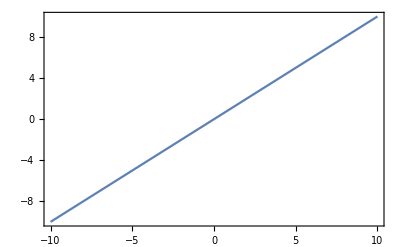

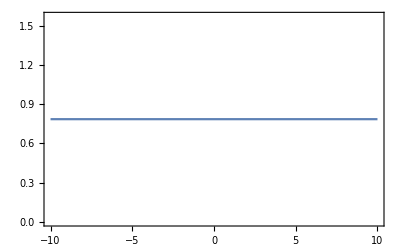

```mathematica
Plot[R[z],{z,-10,10}]
Plot[w[z],{z,-10,10}]


Plot[Re[qInv[z]],{z,-10,10}]
Plot[Im[qInv[z]],{z,-10,10}]


Plot[Re[q[z]],{z,-10,10}]
Plot[Im[q[z]],{z,-10,10}]
```

## straight propagation, scan z and plot complex plane as z increases from far-ve, thru focus, to +ve, 1/q(z) goes CCW in complex plane.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

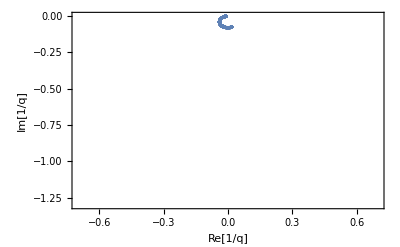

```mathematica
Clear["Global`*"];
λ0=1;
w0=2; (*tightly focused*)
λ=λ0/n;
n=1;

zR=(π w0^2)/λ;
w[z_]:=w0 √(1+ ((λ z)/(π w0^2))^2);
R[z_]:=z(1+((π w0^2)/(λ z))^2);
qInv[z_]:=1/R[z]-I λ0/(π  n  w[z]^2);

q[z_]:=z+zR I;

zEnd=3λ;
zBeg=-100λ;
Cases[Table[{Re[qInv[z]],Im[qInv[z]]},{z,zBeg,zEnd,.01}],x_/;(Head[x[[1]]]==Real)&&(Head[x[[2]]]==Real)];

ListPlot[%,PlotRange->{{-.7,.7},{-1.3,0}},Axes->False,Frame->True,FrameLabel->{"Re[1/q]","Im[1/q]","w0/λ0="<>ToString[w0/λ0]<>", "<>ToString[zBeg]<>"λ to "<>ToString[zEnd]<>"λ"}]
```

## save

-Graphics-

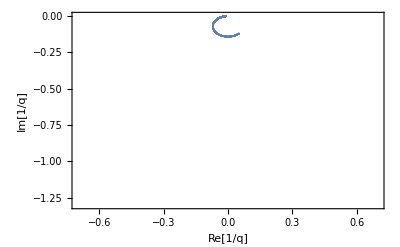

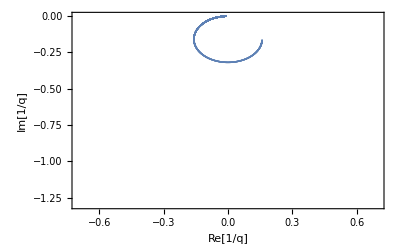

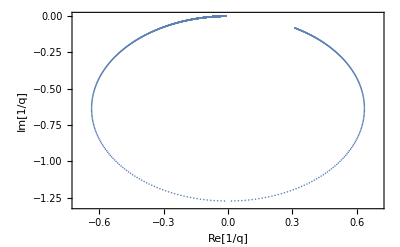

## repeatedly apply propagation matrix for distance Δz

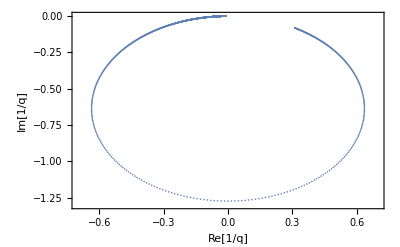

```mathematica
Clear[a,b,c,d];
λ0=1;
w0=.5; (*tightly focused*)
λ=λ0/n;
n=1;

Δz=.01;
mProp={{1,Δz},{0,1}};

{{a,b},{c,d}}=mProp;
qInvi=qInv[zBeg];

data=Reap[Do[
qInvf=1.(c+d qInvi)/(a+b qInvi);
Sow[{Re[ qInvf],Im[ qInvf]}];
qInvi=qInvf
,{z,zBeg,zEnd,Δz}]
][[2,1]];


data2=Cases[%,x_/;(Head[x[[1]]]==Real)&&(Head[x[[2]]]==Real)];

ListPlot[data2,PlotRange->{{-.7,.7},{-1.3,0}},Axes->False,Frame->True,FrameLabel->{"Re[1/q]","Im[1/q]","w0/λ0="<>ToString[w0/λ0]<>", "<>ToString[zBeg]<>"λ to "<>ToString[zEnd]<>"λ"}]
```

## insert various elements in the middle.

```mathematica
Clear[a,b,c,d];
λ0=1;
w0=.5; (*tightly focused*)
λ=λ0/n;
n=1;

zIns=-10;

Δz=.01;
mProp={{1,Δz},{0,1}};
mRef={{1,0},{0,}}
{{a,b},{c,d}}=mProp;
qInvi=qInv[zBeg];

data=Reap[Do[
qInvf=1.(c+d qInvi)/(a+b qInvi);
Sow[{Re[ qInvf],Im[ qInvf]}];
qInvi=qInvf
,{z,zBeg,zEnd,Δz}]
][[2,1]];


data2=Cases[%,x_/;(Head[x[[1]]]==Real)&&(Head[x[[2]]]==Real)];

ListPlot[data2,PlotRange->{{-.7,.7},{-1.3,0}},Axes->False,Frame->True,FrameLabel->{"Re[1/q]","Im[1/q]","w0/λ0="<>ToString[w0/λ0]<>", "<>ToString[zBeg]<>"λ to "<>ToString[zEnd]<>"λ"}]
```

-Graphics-